```mathematica
CreateCities[n_]:=RandomReal[{0,100},{n,2}];
```

```mathematica
cityMap = CreateCities[20];
```

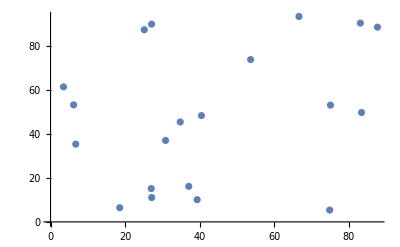

```mathematica
ListPlot[cityMap]
```

```mathematica
OrderingPlot[cityMap_,ordering_]:=Show[
ListPlot[cityMap,AspectRatio->1],
ListLinePlot[cityMap[[ordering]]]
];
```

```mathematica
ListLinePlot[cityMap[[ordering]],AspectRatio->1]
```

```mathematica
ordering = RandomSample[Range[20]]
```

{9,1,7,12,18,15,10,4,14,8,16,3,5,19,13,20,11,17,6,2}

```mathematica
Distace[{{x1_,y1_},{x2_,y2_}}]:=√((x1-x2)^2+(y1-y2)^2);
```

```mathematica
TotalDistance[cityMap_,ordering_]:=Total[Map[Distace,Partition[cityMap[[ordering]],2,1]]];
```

```mathematica
TotalDistance[cityMap,ordering]
```

1082.62

```mathematica
CreatePopulation[n_,cities_ :20]:=Table[RandomSample[Range[cities]],n];
```

```mathematica
population = CreatePopulation[10,20];
```

```mathematica
distances = Map[TotalDistance[cityMap,#]&,CreatePopulation[20,20]]
```

{1020.57,1078.53,1014.88,1123.51,1046.92,1161.48,865.871,733.29,966.188,1011.77,972.498,1069.77,1077.86,947.985,828.943,1152.26,1095.04,1015.72,1159.8,910.37}

```mathematica
Sort[distances]
```

{733.29,828.943,865.871,910.37,947.985,966.188,972.498,1011.77,1014.88,1015.72,1020.57,1046.92,1069.77,1077.86,1078.53,1095.04,1123.51,1152.26,1159.8,1161.48}

```mathematica
ProportionateSelection[cities_,n_]:=RandomVariate[TriangularDistribution[{0,cities},0],n];
```

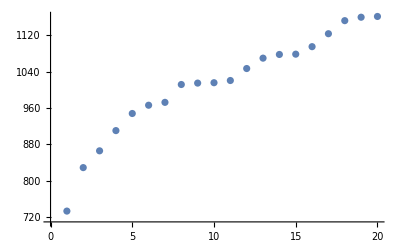

```mathematica
ListPlot[Sort[distances]]
```

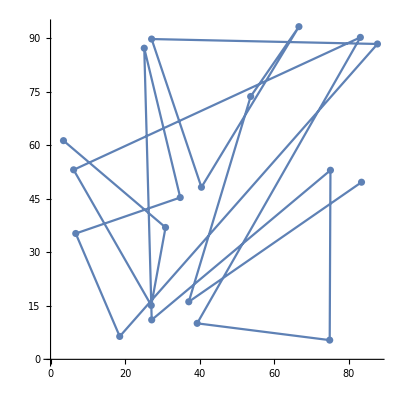
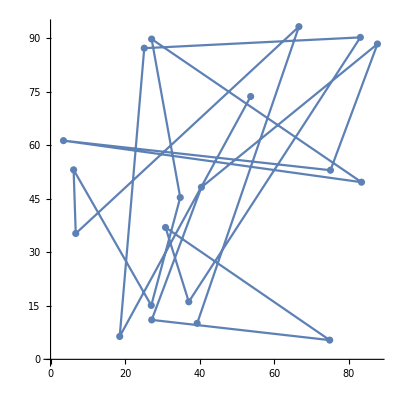
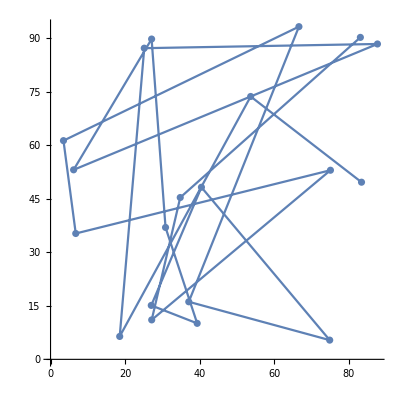
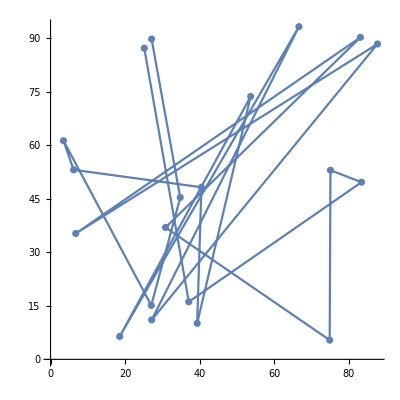
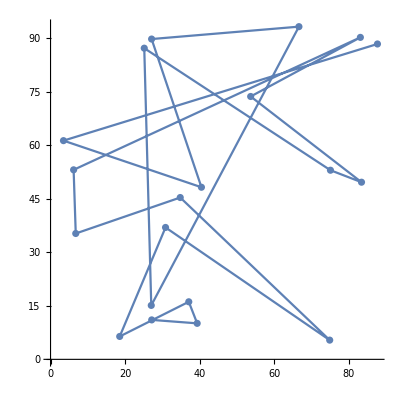
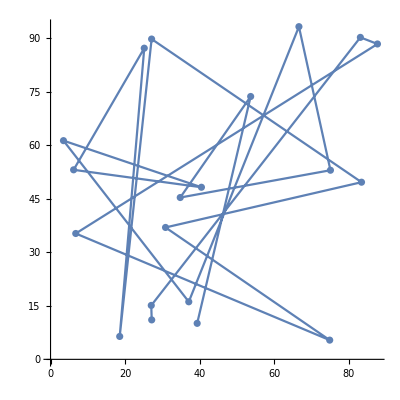
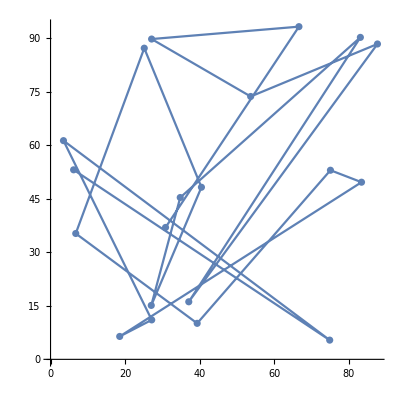
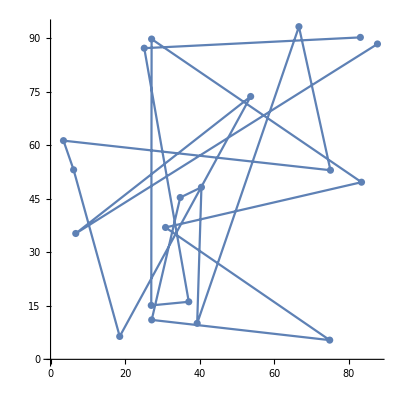

```mathematica
Map[OrderingPlot[cityMap,#]&,population]
```